```mathematica
ClearAll["Global`*"]
ClearSystemCache[]
$PrePrint=MatrixForm;
```

```mathematica
z[n_,ncut_,g_]:=Product[1/((1-Exp[-g j^2])^2), {j,ncut}]+Sum[Exp[-g k^2 n]/(1-Exp[g k^2])Product[If[j≠k, 1/((1-Exp[g(k^2-j^2)])^2),1],{j,ncut}](n+1+1/(1-Exp[-g k^2])+2Sum[If[l≠k,1/(1-Exp[-g(k^2-l^2)]),0],{l,1,ncut}]), {k,ncut}];
f[q_,n_,ncut_,g_]:=Exp[-g q^2]1/(1-Exp[-g q^2]) ^3 *  Product[If[k≠q,1/(1-Exp[-g k^2])^2,1], {k,1,ncut}]  + Exp[-g n q^2]  *  1/(1-Exp[g q^2])  *  Product[If[k≠q, 1/(1-Exp[-g(k^2-q^2)])^2,1], {k,1,ncut}]  *  ( n(n+1)/2 + n 1/(1-Exp[-g q^2])^2 + 
+2(n+1+1/(1-Exp[-g q^2]))  *  Sum[If[l≠q,1/(1-Exp[-g(q^2-l^2)]),0],{l,1,ncut}]
+ Sum[If[l≠q, 1/(1-Exp[-g(l^2-q^2)])^2,0], {l,0,ncut}] + + 2 Sum[If[l≠l' && l≠q &&l'≠q, 1/((1-Exp[-g(q^2-l^2)])(1-Exp[-g(q^2-l'^2)])),0], {l,1,ncut}, {l',1,ncut}] +
+1/2Sum[If[l≠q, 1/Sinh[1/2g(q^2-l^2)]^2,0], {l,1,ncut}]-n/4*1/Sinh[1/2g q^2]^2) + 
+ Sum[If[p≠q, Exp[-g n p^2]  *   Exp[- g(q^2 -p^2)]  *  1/((1-Exp[-g(q^2-p^2)])(1-Exp[g p^2]))  *  
Product[If[k≠p, 1/(1-Exp[-g (k^2 -p^2)])^2, 1], {k,1,ncut}]  *  (n + 1/(1-Exp[-g (p^2-q^2)]) + 1/(1-Exp[-g p^2]) +
+ 2Sum[If[l≠p, 1/(1-Exp[-g(p^2-l^2)]),0], {l,1,ncut}]),0], {p,1,ncut}];
Izero[n_,ncut_,g_]:=Sum[Exp[-g(n-1)p^2]  *  Product[If[k ≠p, 1/(1-Exp[-g(k^2-p^2)])^2,1], {k,0,ncut}]  *  (n+2Sum[If[l≠p,1/(1-Exp[-g(p^2-l^2)]),0], {l,0,ncut}]), {p,0,ncut}];
```

```mathematica
Corr[x_,n_,ncut_,g_]:=1/z[n,ncut,g]*(Izero[n,ncut,g]+2Sum[Cos[2Pi*q*x]*f[q,n,ncut,g], {q,1,20}])/n
```

```mathematica
X=Table[i/100, {i,-50,50}];
Y=Table[Corr[X[[i]],100,20,0.03625], {i,1,Length[X]}];
data=Table[{X[[i]],Y[[i]]}, {i,1,Length[X]}];
```

General::munfl: -1.90852×10^-269 9.49632×10^-43 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-815.625] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

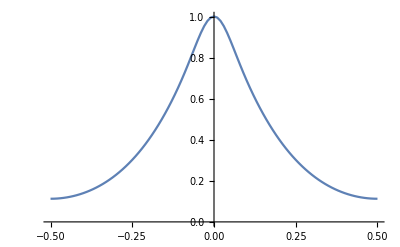

```mathematica
ListPlot[data, Joined->True]
```